## Cographs and Endographs

### Introduction

This Mathematica notebook is licensed under a  .

It provides software for producing the cograph and the endograph of functions from the reals to the reals.   gives a description of this work.

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.  
 
Charles Wells

### RealCograph

```mathematica
Remove[Env]
```

To produce a robust package, this definition of RealCograph should be turned into a module incorporating the definition of Tikk and Tixx.

```mathematica
Tikk[x_,y_]:=Line[{{x,y-.05},{x,y+.05}}];
Tixx[a_,b_,c_,n_]:=Table[Tikk[a+k n,c],{k,0,(b-a)/n}]
```

```mathematica
Options[RealCograph]={ArrowSource->2,ArrowTarget->0,SampleIncrement->1/2,ArrowHeadSize->.015,TikkIncrement->1/4,LabelIncrement->1,ArrowColor->Blue,ImageSize->Large}
```

{ArrowSource→2,ArrowTarget→0,SampleIncrement→1/2,ArrowHeadSize→0.015,TikkIncrement→1/4,LabelIncrement→1,ArrowColor→RGBColor[0, 0, 1],ImageSize→Large}

```mathematica
RealCograph[DisplayLeft_,DisplayRight_,DomainLeft_,DomainRight_,Func_ ,OptionsPattern[]] :=(LabelOffset:=(1/10)(OptionValue[ArrowSource]-OptionValue[ArrowTarget]);
Show[Graphics[Line[{{DisplayLeft,OptionValue[ArrowSource]},{DisplayRight,OptionValue[ArrowSource]}}]],Graphics[Line[{{DisplayLeft,OptionValue[ArrowTarget]},{DisplayRight,OptionValue[ArrowTarget]}}]],Graphics[Tixx[DisplayLeft,DisplayRight,OptionValue[ArrowTarget],OptionValue[TikkIncrement]]],Graphics[Tixx[DisplayLeft,DisplayRight,OptionValue[ArrowSource],OptionValue[TikkIncrement]]],Graphics[Text[#,{#,OptionValue[ArrowSource]+LabelOffset}]&/@Table[n,{n,DisplayLeft,DisplayRight,OptionValue[LabelIncrement]}]],Graphics[Text[#,{#,OptionValue[ArrowTarget]-LabelOffset}]&/@Table[n,{n,DisplayLeft,DisplayRight,OptionValue[LabelIncrement]}]],Graphics[{OptionValue[ArrowColor],Arrowheads[OptionValue[ArrowHeadSize]],Table[Arrow[{{x,OptionValue[ArrowSource]},{Func[x],OptionValue[ArrowTarget]}}],{x,DomainLeft,DomainRight,OptionValue[SampleIncrement]}]}]
])
```

### Real Endograph

```mathematica
Tikk[x_,y_]:=Line[{{x,y-.05},{x,y+.05}}];
Tixx[a_,b_,c_,n_]:=Table[Tikk[a+k n,c],{k,0,(b-a)/n}]
```

```mathematica
Arr[a_,c_,Envelope_:0]:=(jump:=c-a;adjust:=.25;htadj:=3;Arrow[BezierCurve[{{a,0},{a+ adjust jump,2+Envelope},
{c- adjust jump,2+Envelope},{c,0}}]])
```

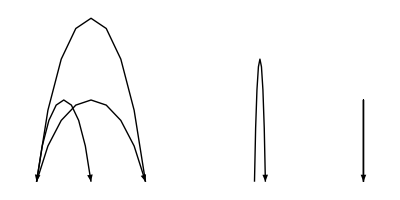

```mathematica
Show[Graphics[{Arr[3,3],Arr[1,1.2,1],Arr[-1,-3,2],Arr[-3,-1],Arr[-3,-2]}],ImageSize->Tiny]
```

```mathematica
Options[RealEndograph]={SampleIncrement->1/2,ArrowHeadSize->.015,TikkIncrement->1/4,LabelIncrement->1,ArrowColor->Blue,Env->.2Abs[x]}
```

{SampleIncrement→1/2,ArrowHeadSize→0.015,TikkIncrement→1/4,LabelIncrement→1,ArrowColor→RGBColor[0, 0, 1],Env→0.2 Abs[x]}

```mathematica
RealEndograph[DisplayLeft_,DisplayRight_,DomainLeft_,DomainRight_,Func_,OptionsPattern[]]:=Show[Graphics[Line[{{DisplayLeft,0},{DisplayRight,0}}]],Graphics[Tixx[DisplayLeft,DisplayRight,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,DisplayLeft,DisplayRight}]],Graphics[{OptionValue[ArrowColor],Arrowheads[OptionValue[ArrowHeadSize]],Table[Arr[x,Func[x],OptionValue[Env]],{x,DomainLeft,DomainRight,OptionValue[SampleIncrement]}]}],ImageSize->Large]
```

### Examples

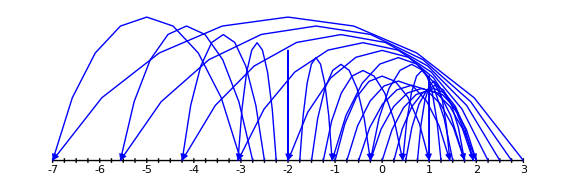

```mathematica
RealEndograph[-7,3,-3,3,udpar,Env->.4Abs[x^1.5],SampleIncrement->1/4]
```

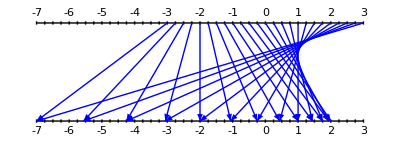

```mathematica
RealCograph[-7,3,-3,3,udpar,SampleIncrement->1/4,ArrowSource->3,ImageSize->Medium,ArrowHeadSize->.022]
```

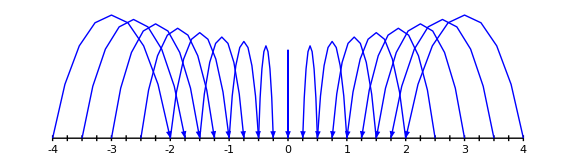

```mathematica
RealEndograph[-4,4,-4,4,.5#&,Env->.2Abs[x]]
```

### Examples

```mathematica
first[x_]:=.5x
```

```mathematica
RealEndograph[-4,4,-4,4,first]
```

-Graphics-

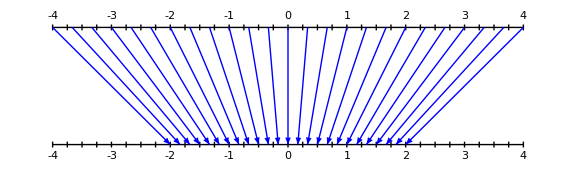

```mathematica
RealCograph[-4,4,-4,4,first,SampleIncrement->1/3]
```

```mathematica
f2[x_]:=2x
```

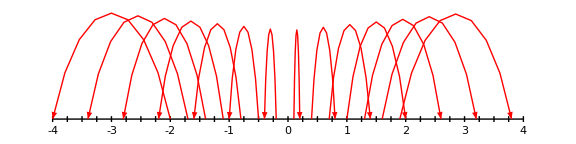

```mathematica
RealEndograph[-4,4,-2,2,f2,SampleIncrement->.3,ArrowColor->Red]
```

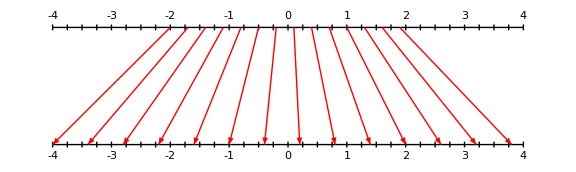

```mathematica
RealCograph[-4,4,-2,2,f2,SampleIncrement->.3,ArrowColor->Red]
```

```mathematica
f3[x_]:=x+1
```

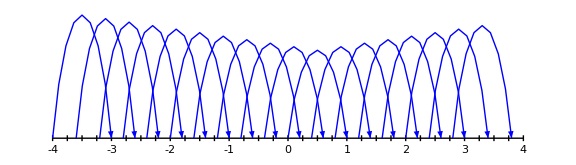

```mathematica
RealEndograph[-4,4,-4,3,f3,SampleIncrement->.4]
```

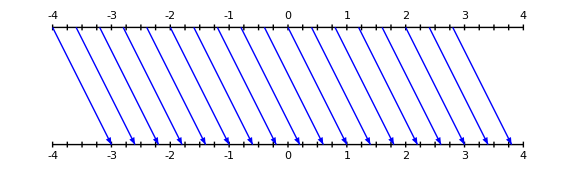

```mathematica
RealCograph[-4,4,-4,3,f3,SampleIncrement->.4]
```

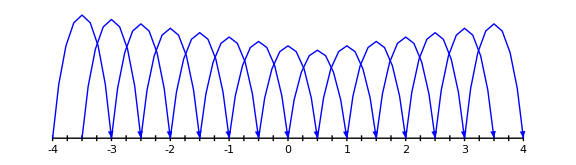

```mathematica
RealEndograph[-4,4,-4,3,f3,SampleIncrement->1/2]
```

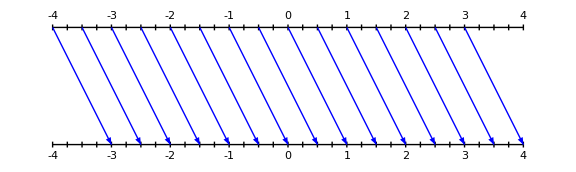

```mathematica
RealCograph[-4,4,-4,3,f3,SampleIncrement->1/2]
```

```mathematica
k[x_]:=Sqrt[x+4]
```

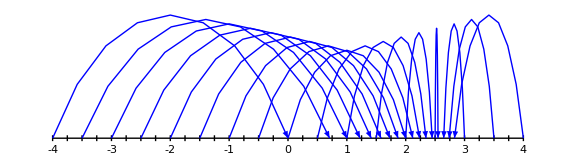

```mathematica
RealEndograph[-4,4,-4,4,k]
```

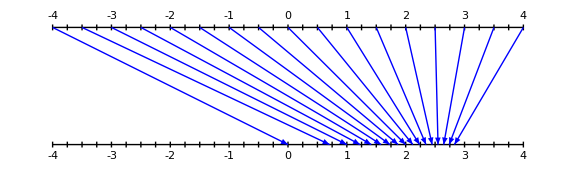

```mathematica
RealCograph[-4,4,-4,4,k]
```

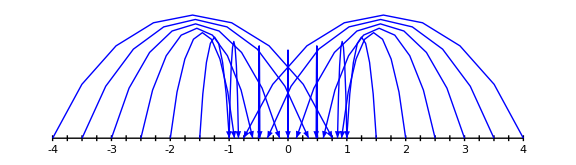

```mathematica
RealEndograph[-4,4,-4,4,Sin]
```

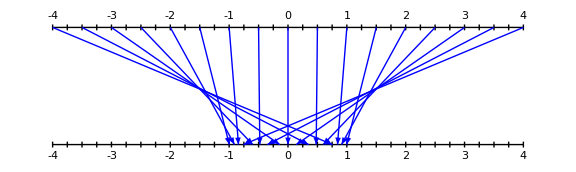

```mathematica
RealCograph[-4,4,-4,4,Sin]
```

```mathematica
vv[x_]:=x^2
```

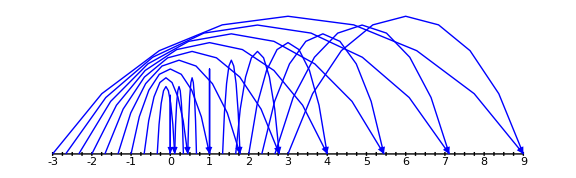

```mathematica
RealEndograph[-3,9,-3,3,vv,SampleIncrement->1/3,Env->0.9Abs[x]]
```

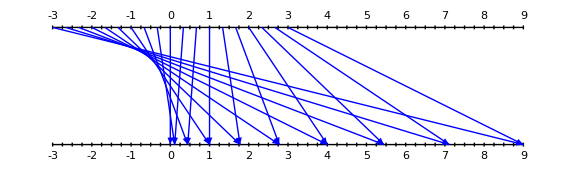

```mathematica
RealCograph[-3,9,-3,3,vv,SampleIncrement->1/3,ArrowSource->3]
```

```mathematica
udpar[x_]:=2-x^2
```

```mathematica
ccc[x_]:=x^3
```

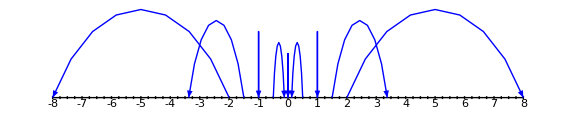

```mathematica
RealEndograph[-8,8,-2,2,#^3&,SampleIncrement->1/2,Env->Abs[x]]
```

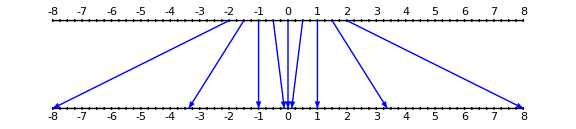

```mathematica
RealCograph[-8,8,-2,2,ccc,SampleIncrement->1/2,ArrowSource->3]
```

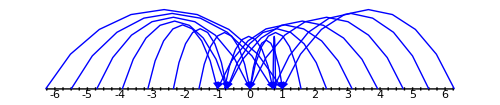

```mathematica
(*DON'T DELETE THIS*)Show[Graphics[Line[{{-2Pi,0},{2 Pi,0}}]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-6,6}]],Graphics[{Blue,Arrowheads[.02],Table[Arr[x,Cos[x],0.2Abs[x]],{x,-2 Pi,2 Pi,Pi/4}]}],ImageSize->500]
```

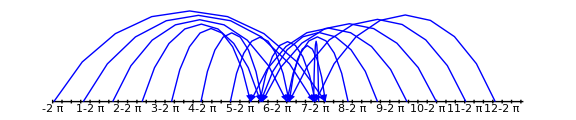

```mathematica
RealEndograph[-2Pi,2Pi,-6.25,6.25,Cos,SampleIncrement->Pi/4]
```

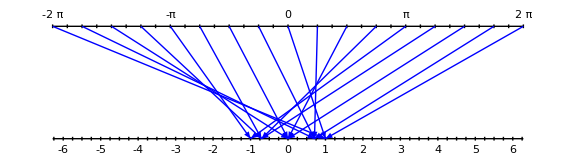

```mathematica
Show[Graphics[Line[{{-2Pi,3},{2Pi,3}}]],Graphics[Line[{{-2Pi,0},{2Pi,0}}]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Tixx[-2Pi,2Pi,3,Pi/8]],Graphics[Text[#,{#,3.3}]&/@Table[n,{n,-2Pi,2Pi,Pi}]],Graphics[Text[#,{#,-0.3}]&/@Table[n,{n,-6,6,1}]],Graphics[{Blue,Arrowheads[.015],Table[Arrow[{{x,3},{Cos[x],0}}],{x,-2Pi,2Pi,Pi/4}]}],ImageSize->Large]
```

```mathematica
vv[x_]:=(1/7)(x-1)^2
```

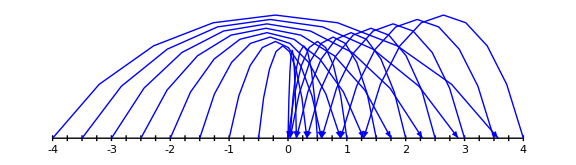

```mathematica
RealEndograph[-4,4,-4,4,vv,SampleIncrement->1/2]
```

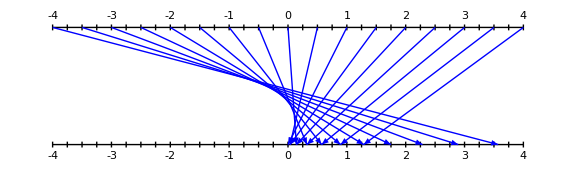

```mathematica
RealCograph[-4,4,-4,4,vv,SampleIncrement->1/2,ArrowSource->2] (*What is that envelope?*)
```

```mathematica
ww[x_]:=(1/16)x^3
```

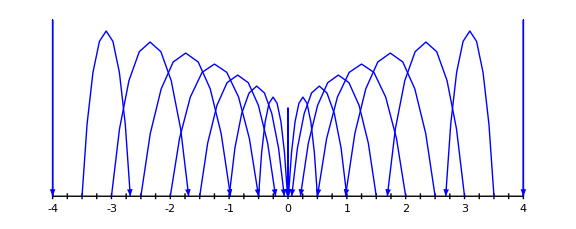

```mathematica
RealEndograph[-4,4,-4,4,ww,SampleIncrement->1/2, Env->.5Abs[x]]
```

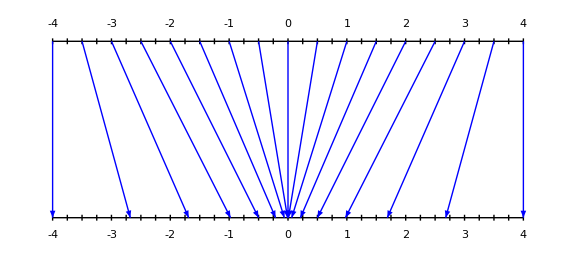

```mathematica
RealCograph[-4,4,-4,4,ww,SampleIncrement->1/2,ArrowSource->3]
```

```mathematica
ww2[x_]:=(x+2)/2
```

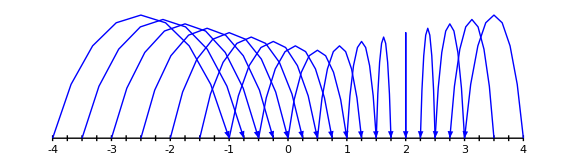

```mathematica
RealEndograph[-4,4,-4,4,ww2,SampleIncrement->1/2]
```

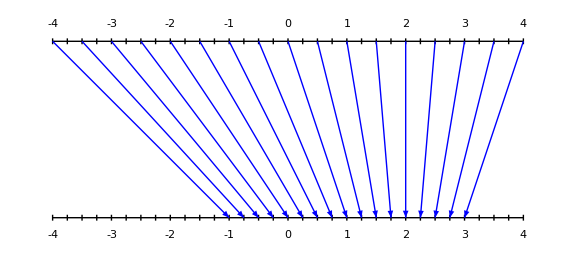

```mathematica
RealCograph[-4,4,-4,4,ww2,SampleIncrement->1/2,ArrowSource->3]
```

```mathematica
ww3[x_]:=x+.3Sin[x]+.2
```

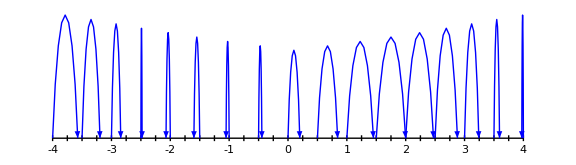

```mathematica
RealEndograph[-4,4,-4,4,ww3,SampleIncrement->1/2]
```

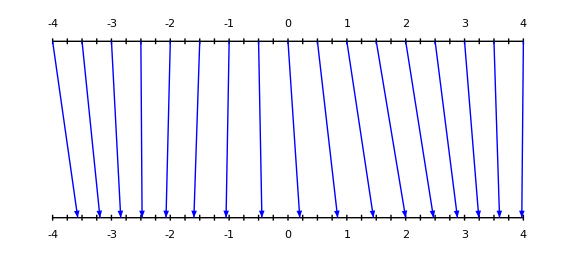

```mathematica
RealCograph[-4,4,-4,4,ww3,SampleIncrement->1/2,ArrowSource->3]
```

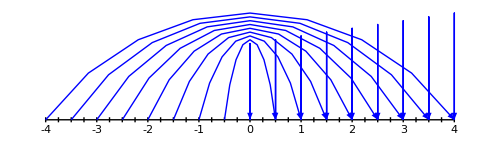

```mathematica
Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Blue,Arrowheads[.02],Table[Arr[x,Abs[x],0.2Abs[x]],{x,-4,4,1/2}]}]]
```

```mathematica
ww4[x_]:=Abs[x]
```

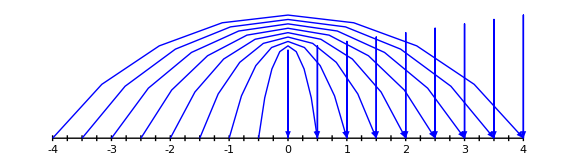

```mathematica
RealEndograph[-4,4,-4,4,ww4,SampleIncrement->1/2]
```

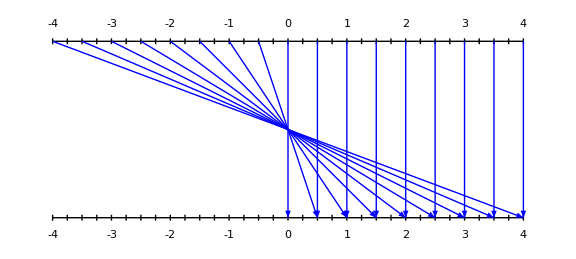

```mathematica
RealCograph[-4,4,-4,4,ww4,SampleIncrement->1/2,ArrowSource->3]
```

```mathematica
ww5[x_]:=ArcTan[x]
```

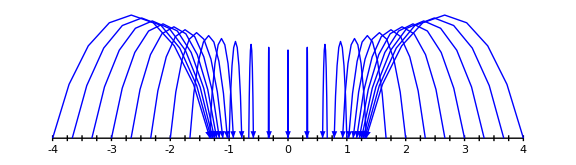

```mathematica
RealEndograph[-4,4,-4,4,ww5,SampleIncrement->1/3]
```

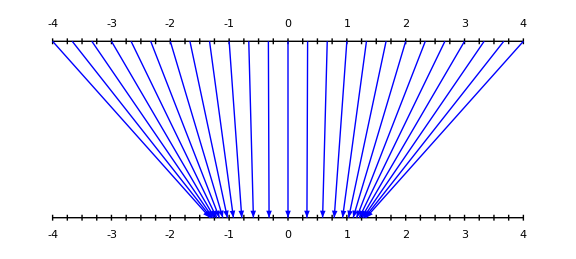

```mathematica
RealCograph[-4,4,-4,4,ww5,SampleIncrement->1/3,ArrowSource->3]
```

```mathematica
ww6[x_]:=If[x==0,0,1/x]
```

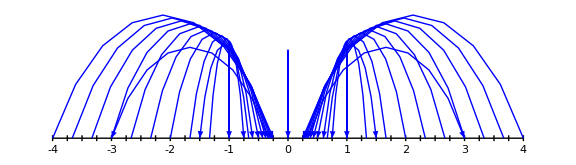

```mathematica
RealEndograph[-4,4,-4,4,ww6,SampleIncrement->1/3]
```

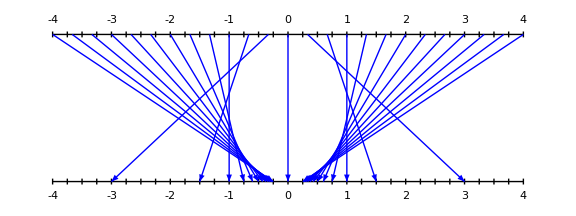

```mathematica
RealCograph[-4,4,-4,4,ww6,SampleIncrement->1/3,ArrowSource->2.5]
```

```mathematica
ww7[x_]:=If[x==0,0,1/(x^2)]
```

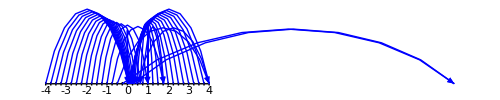

```mathematica
(*DONT DELETE*)Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Blue,Arrowheads[.02],Table[Arr[x,ww7[x],0.2Abs[x]],{x,-4,4,1/4}]}]]
```

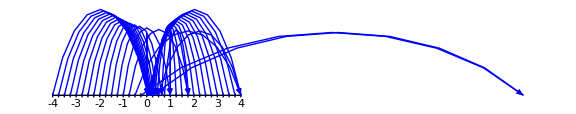

```mathematica
RealEndograph[-4,4,-4,4,ww7,SampleIncrement->1/4]
```

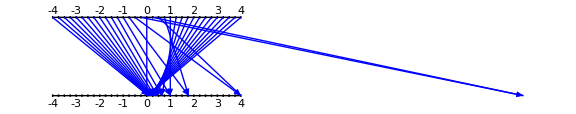

```mathematica
RealCograph[-4,4,-4,4,ww7,SampleIncrement->1/4,ArrowSource->3]
```

### Some experiments

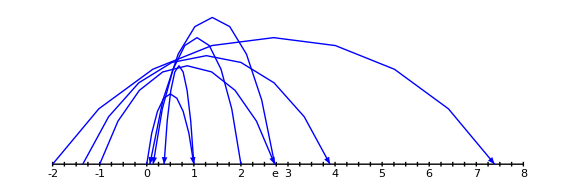

```mathematica
Show[Graphics[Line[{{-2,0},{8,0}}]],Graphics[Tixx[-2,8,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-2,8}]],
Graphics[Text["e",{E,-0.2}]],Graphics[{Blue,Arrowheads[.02],Table[Arr[x,E^(-x),0.8Abs[x]],{x,{-2,-E/2,-1,0,1,2,E}}]}],ImageSize->Large]
```

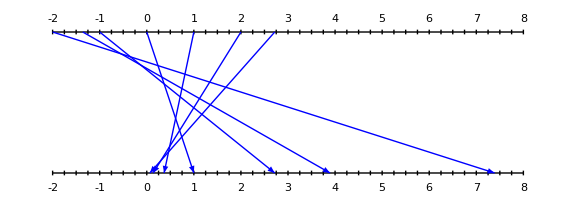

```mathematica
Show[Graphics[Line[{{-2,3},{8,3}}]],Graphics[Line[{{-2,0},{8,0}}]],Graphics[Tixx[-2,8,0,1/4]],Graphics[Tixx[-2,8,3,1/4]],Graphics[Text[#,{#,3.3}]&/@Table[n,{n,-2,8}]],Graphics[Text[#,{#,-0.3}]&/@Table[n,{n,-2,8}]],Graphics[{Blue,Arrowheads[.015],Table[Arrow[{{x,3},{E^(-x),0}}],{x,{-2,-E/2,-1,0,1,2,E}}]}],ImageSize->Large]
```

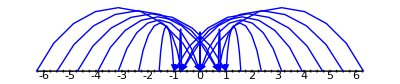

```mathematica
Show[Graphics[Line[{{-2Pi,0},{2 Pi,0}}]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-6,6}]],Graphics[{Blue,Arrowheads[.015],Table[Arr[x,Sin[x],0.2Abs[x]],{x,-2 Pi,2 Pi,Pi/4}]}]]
```

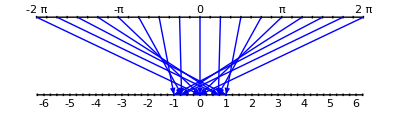

```mathematica
Show[Graphics[Line[{{-2Pi,3},{2Pi,3}}]],Graphics[Line[{{-2Pi,0},{2Pi,0}}]],Graphics[Tixx[-2Pi,2Pi,3,Pi/8]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Text[#,{#,3.3}]&/@Table[n,{n,-2Pi,2Pi,Pi}]],Graphics[Text[#,{#,-0.3}]&/@Table[n,{n,-6,6,1}]],Graphics[{Blue,Arrowheads[.015],Table[Arrow[{{x,3},{Sin[x],0}}],{x,-2Pi,2Pi,Pi/4}]}]]
```

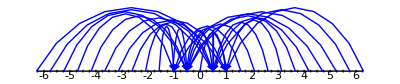

```mathematica
Show[Graphics[Line[{{-2Pi,0},{2 Pi,0}}]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-6,6}]],Graphics[{Blue,Arrowheads[.015],Table[Arr[x,Cos[2x],0.2Abs[x]],{x,-2 Pi,2 Pi,Pi/6}]}]]
```

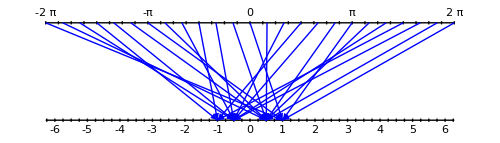

```mathematica
Show[Graphics[Line[{{-2Pi,3},{2Pi,3}}]],Graphics[Line[{{-2Pi,0},{2Pi,0}}]],Graphics[Tixx[-2Pi,2Pi,3,Pi/8]],Graphics[Tixx[-6.25,6.25,0,1/4]],Graphics[Text[#,{#,3.3}]&/@Table[n,{n,-2Pi,2Pi,Pi}]],Graphics[Text[#,{#,-0.3}]&/@Table[n,{n,-6,6,1}]],Graphics[{Blue,Arrowheads[.015],Table[Arrow[{{x,3},{Cos[ 2x],0}}],{x,-2Pi,2Pi,Pi/6}]}]]
```

### Powers of functions (stub)

```mathematica
Remove[g]
```

```mathematica
g[x_]:=4x(1-x)
```

```mathematica
g[(5-Sqrt[5])/8]
```

1/2 (5-√5) (1+1/8 (-5+√5))

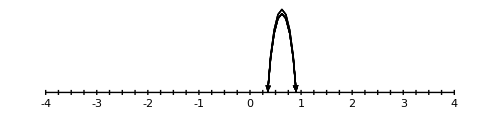

```mathematica
(start:=(5-Sqrt[5])/8;
Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Arrowheads[.02],Table[Arr[x,g[x],0.2Abs[x]],{x,{start,start//g,start//g//g,start//g//g//g,start//g//g//g//g,start//g//g//g//g//g,start//g//g//g//g//g//g,start//g//g,start//g//g//g//g//g//g//g//g}}]}]])
```

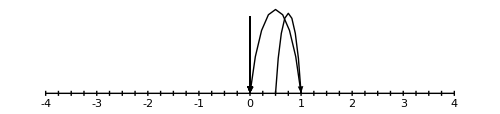

```mathematica
(start:=1/2;
Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Arrowheads[.02],Table[Arr[x,g[x],0.2Abs[x]],{x,{start,start//g,start//g//g,start//g//g//g,start//g//g//g//g,start//g//g//g//g//g,start//g//g//g//g//g//g,start//g//g,start//g//g//g//g//g//g//g//g}}]}]])
```

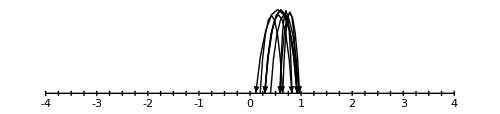

```mathematica
(start:=1/5;
Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Arrowheads[.02],Table[Arr[x,g[x],0.2Abs[x]],{x,{start,start//g,start//g//g,start//g//g//g,start//g//g//g//g,start//g//g//g//g//g,start//g//g//g//g//g//g,start//g//g,start//g//g//g//g//g//g//g//g}}]}]])
```

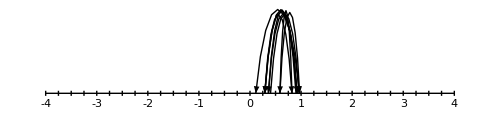

```mathematica
(start:=.9;
Show[Graphics[Line[{{-4,0},{4,0}}]],Graphics[Tixx[-4,4,0,1/4]],Graphics[Text[#,{#,-0.2}]&/@Table[n,{n,-4,4}]],Graphics[{Arrowheads[.02],Table[Arr[x,g[x],0.2Abs[x]],{x,{start,start//g,start//g//g,start//g//g//g,start//g//g//g//g,start//g//g//g//g//g,start//g//g//g//g//g//g,start//g//g,start//g//g//g//g//g//g//g//g}}]}]])
```